General::munfl: Exp[-722.502] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-950.627] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1210.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

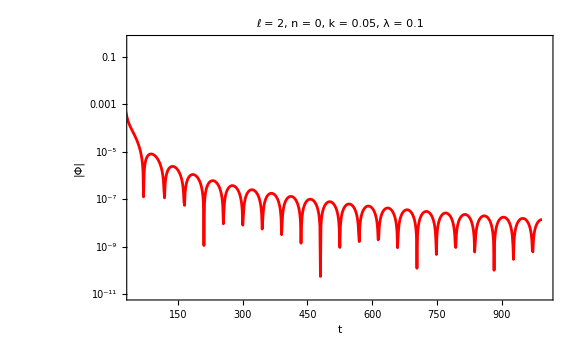

TimeProfile1.pdf

```mathematica
ClearAll["Global`*"]

(* ===Metric and potential===*)

f[r_,k_,λ_]:=1/(1-k)-2/r+(λ/r) Log[r/λ]

dfdr[r_,k_,λ_]:=2/r^2+(λ/r^2) (1-Log[r/λ])

Veff[r_,l_,μ_,k_,λ_]:=Module[{fr,dfr},fr=f[r,k,λ];
dfr=dfdr[r,k,λ];
fr*((l (l+1))/r^2+dfr/r+μ^2)]

horizonRadius[k_,λ_]:=r/. FindRoot[f[r,k,λ]==0,{r,1}]

(* ===Parameters===*)

μ=0.1;
l=2;
k=0.05*0;
λ=0.0000000002;

umin=0;umax=1000;
vmin=10^-5;vmax=200;

n=800;
h=(umax-umin)/n;

(* ===Initialize grid===*)

Y=ConstantArray[0,{n+1,n+1}];

vc=4.0;
vl=2.0;

(*Horizon*)

rH=horizonRadius[k,λ];

(*Tortoise inversion (simple shift like your Python code)*)

rOfrs[rs_]:=rs+1.654;

(* ===Initial Gaussian pulse===*)

Do[v=vmin+j h;
Y[[1,j+1]]=Exp[-10 (v-vc)^2];
If[Abs[Y[[1,j+1]]]<10^-64,Y[[1,j+1]]=0];
Y[[j+1,j+1]]=0;,{j,0,n}]

(* ===Time evolution===*)

Do[Do[u=umin+i h;
v=vmin+j h;
rs=(v-u)/2;
rr=rOfrs[rs];
VS=Veff[rr,l,μ,k,λ];
YS=Y[[i,j]];
YE=Y[[i,j+1]];
YW=Y[[i+1,j]];
Y[[i+1,j+1]]=(YE+YW) (1-h^2 VS/16)-YS;,{j,i+1,n}],{i,1,n}]

(* ===Extract waveform at fixed radius===*)

rsObs=5;

dataT={};
dataPsi={};

Do[v=vmin+i h;
u=v-2 rsObs;
iu=Floor[(u-umin)/h]+1;
iv=Floor[(v-vmin)/h]+1;
If[1<=iu<=n&&1<=iv<=n,t=(u+v)/2;
AppendTo[dataT,t];
AppendTo[dataPsi,Abs[Y[[iu,iv]]]];];,{i,1,n+1}]

(* ===Plot waveform===*)

ListLinePlot[Transpose[{dataT,dataPsi}],ScalingFunctions->{"Linear","Log"},PlotStyle->Red,Frame->True,FrameLabel->{"t","|Φ|"},PlotRange->{{50,1000},All},GridLines->Automatic,PlotLabel->Row[{"ℓ = 2,  n = 0,  k = 0.05,  λ = 0.1"}],ImageSize->Large]

Export["TimeProfile1.pdf",%]
```